```mathematica
SetDirectory[NotebookDirectory[]];
<<model.m;
```

#### BTZ case

S[l]=L/(2 G_3)Log[(2zh)/ϵ_UV Sinh[l/(2zh)]]

```mathematica
S[l_]:=Log[(2zh)/Subscript[ϵ, UV] Sinh[l/(2zh)]];
```

```mathematica
Dynamic[ListPlot[out[[All,All,1]],Joined->True]]
```

```mathematica
lzt={findlzt[S[l]]};
out = geogen[lzt];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.998711}. NIntegrate obtained 7.14337-3.18219 ⅈ and 0.0664485 for the integral and error estimates.

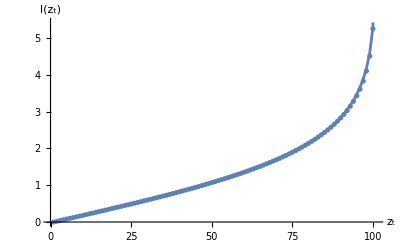

```mathematica
Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];

Show[ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[%]]
```

#### Power interpolation case

S[l]=L/(2 G_3)Log[(2 zh)/ϵ_UV (l/(2zh) +ⅇ^(l/(2 zh))(l/(2zh))^p)/(1+ (l/(2zh))^p)]

```mathematica
S[l_]:=Log[(2 zh)/Subscript[ϵ, UV] (l/(2zh) +ⅇ^(l/(2 zh))(l/(2zh))^s)/(1+ (l/(2zh))^s)];
```

```mathematica
Dynamic[ListPlot[out[[All,All,1]],Joined->True]]
```

```mathematica
lzt=Table[findlzt[S[l]/.s->0.1i+2  ],{i,0,23}];
out = geogen[lzt];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.988125}. NIntegrate obtained 8.64134-3.23901 ⅈ and 0.0502711 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.999827665716657}. NIntegrate obtained 8.90004-6.83015 ⅈ and 0.802693 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {0.988281}. NIntegrate obtained 8.67214-3.03607 ⅈ and 0.287379 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

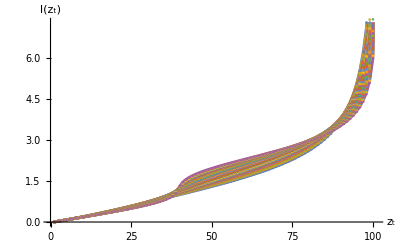

```mathematica
Table[NIntegrate[(2 z)/(√(-z^2 +z0^2))1/(√f[z])/.f->Function[{z1},Interpolation[Transpose[{Table[i,{i,0,1,0.01}][[;;Length[out[[j]]]]],out[[j,All,1]]}]][z1]],{z,0,z0}],{j,Length[out]},{z0,0,1,0.01}];

Show[ListPlot[lzt[[All,All,1]],AxesLabel->{Subscript[z, t],l[Subscript[z, t]]},Joined->True],ListPlot[%]]
```